## Definitions

```mathematica
paramInEllipsoidQ[θ_,θStar_,cov_] := Module[{x, invMat},
	x = θ - θStar;
	invMat = Inverse[cov];
	x.invMat.x < 1
]
```

```mathematica
(*This is from Reichl et al 2020*)
getEllDraw[θStar_,cov_] := Module[
	{k, rs, pt, λs, λh, eVals, eVecs},
	k = Length@cov;
	rs = RandomVariate[UniformDistribution[]];
	pt = RandomVariate[NormalDistribution[], k];
	λs = Total[pt^2];
	λh = rs^(1/k)/√λs;
	eVals = Eigenvalues[MatrixPower[cov, 1/2]];
	eVecs = Eigenvectors[MatrixPower[cov, 1/2]];
	(λh pt eVals).eVecs + θStar
]
```

## Tests

### Ellipsoid Geometry tests

```mathematica
θStar={0.5,0.5};cov={{0.1,0.08},{0.08,0.2}};
MatrixForm[cov]
```

(0.1 | 0.08
0.08 | 0.2)

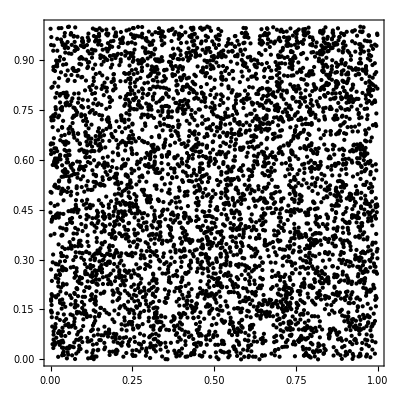

```mathematica
randomPoints=RandomVariate[UniformDistribution[10000]]//Partition[#,2]&;
colors=Table[If[paramInEllipsoidQ[p,θStar,cov],Red,Blue],{p,randomPoints}];
Graphics[
Point[randomPoints,VertexColors->colors],AspectRatio->1,ImagePadding->20,Frame->True]
```

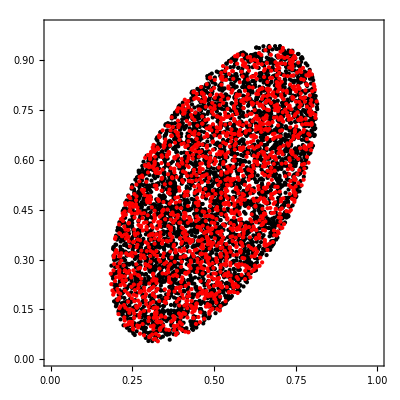

```mathematica
randomPoints2=Table[getEllDraw[θStar,cov],4000];
Graphics[
{
Black,Point[randomPoints2],
Red,Point[Select[randomPoints,paramInEllipsoidQ[#,θStar,cov]&]]
},
AspectRatio->1,ImagePadding->20,Frame->True,PlotRange->{{0,1},{0,1}}
]
```